TOV case. Equation of state: p = κ_0 ρ^2 , taken from arXiv:0309041, with κ_0= 4.012 × 10^-4 fm^3/MeV.
We use R, p and ρ have dimension of an inverse square length. In this way κ_0= 2.5 × 10^2 km^2.
We make everything dimensionless by normalising to half the gravitational radius of the Sun r_0= 1.47664 km. Therefore κ_0= 115.

```mathematica
kappa0=115
```

115

```mathematica
TOVeqs[rho0_]:=NDSolve[{kappa0*rho'[r]+(M[r]/(2r^2))*(1+kappa0*rho[r])*(1+4*Pi*r^3*kappa0*rho[r]^2/M[r])*(1-2M[r]/r)^(-1)==0,M'[r]==4Pi*rho[r]*r^2,rho[0.001]==rho0,M[0.001]==4Pi*rho0*(0.001)^3/3},{rho,M},{r,0.001,30}]
```

```mathematica
TOVeqs[0.01]
```

{{rho→InterpolatingFunction[{{0.001, 30.}}, <>],M→InterpolatingFunction[{{0.001, 30.}}, <>]}}

```mathematica
rhoTOV[r_,rho0_]:=rho[r]/.TOVeqs[rho0]
```

```mathematica
MassTOV[r_,rho0_]:=M[r]/.TOVeqs[rho0]
```

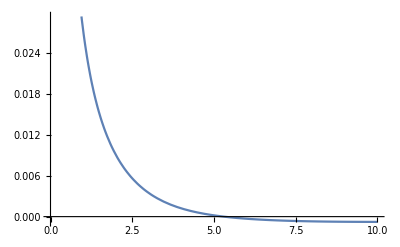

```mathematica
Plot[{rhoTOV[x,10]},{x,0.001,10}]
```

```mathematica
Rstar[rho0_]:=FindRoot[rhoTOV[r,rho0]==0,{r,0.001,20}][[1,2]]
```

```mathematica
Rstar[0.01]
```

6.24755

```mathematica
Mstar[rho0_]:=MassTOV[Rstar[rho0],rho0][[1]]
```

```mathematica
Mstar[0.01]
```

1.9308

```mathematica
DataMstarRStar=Table[{1.47664*Rstar[10^i],Mstar[10^i]},{i,-4,-1,0.1}];
```

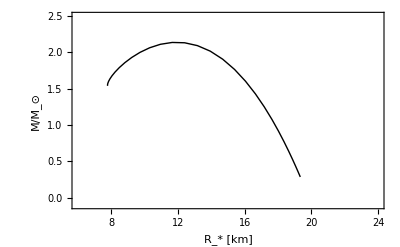

```mathematica
StabTOV=ListLinePlot[DataMstarRStar,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"R_* [km]","M/M_⊙"},LabelStyle->Medium,PlotRange->{{6,24},{-0.1,2.5}}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oliverpiattella/Dropbox/Work/Pedro/DissArticlePedro

```mathematica
Export["StabTOV.eps",StabTOV]
```

StabTOV.eps